```mathematica
(* processing selection sort times *)
data = Import["/Users/john/structures/assignment2/csv_outputs/linear.csv", "CSV"];
wordCounts = data[[All, 1]];
comparisons = data[[All, 2]];
swaps = data[[All, 3]];
times = data[[All, 4]];
```

```mathematica
"
```

0.124765+1.87601×10^-6 words-6.10365×10^-12 words^2

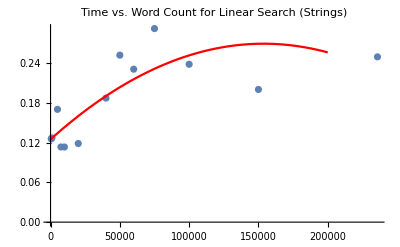

Set::write: Tag List in {8718, 120463, 1536458, 2392228, 260969, 3914910, 561860, 3858, 55237, 718243, 877144, 87195, 1121154}[words_] is Protected.

-62209.2+16.5153 words

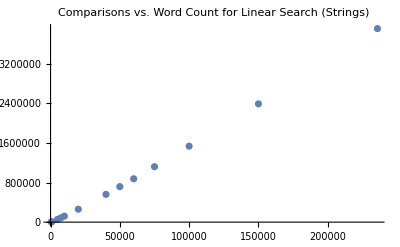

```mathematica
time[words_] = Fit[Transpose[{wordCounts, times}], {1, words, words^2}, words]

Show[ListPlot[Transpose[{wordCounts, times}]], Plot[time[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Time vs. Word Count for Linear Search (Strings)"]

comparisons[words_] = Fit[Transpose[{wordCounts, comparisons}], {1, words}, words]

Show[ListPlot[Transpose[{wordCounts, comparisons}]], Plot[comparisons[words], {words, 0, 200000}, PlotStyle->Red], PlotLabel->"Comparisons vs. Word Count for Linear Search (Strings)"]
```